# ESSENTIAL CALCULUS SECOND EDITION JAMES STEWART

## CHAPTER 3 APPLICATIONS OF DIFFERENTIATION

3.1 MAXIMUM AND MINIMUM VALUES

## DEFINITION 1

### -Graphics-

### -Graphics-

## DEFINITION 2

### -Graphics-

### -Graphics--Graphics-

## EXAMPLE 1

### -Graphics-

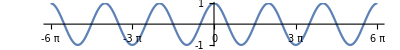

```mathematica
Plot[Cos[x],{x,-6Pi,6Pi},Ticks->{Table[n*Pi,{n,-6,6}],{-1,1}},AspectRatio->1/8]
```

## EXAMPLE 2

### -Graphics--Graphics-

## EXAMPLE 3

### -Graphics--Graphics-

## EXAMPLE 4

### -Graphics-

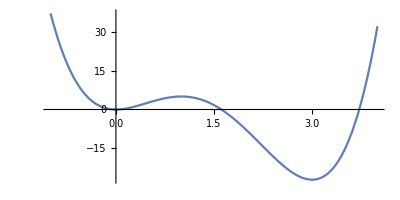

5

37

0

-27

32

```mathematica
Clear[f]
Clear[x]
f[x_]=3 x^4-16 x^3+18 x^2;
Plot[f[x],{x,-1,4},AspectRatio->1/2]
f[1]
f[-1]
f[0]
f[3]
f[4]
```

## THE EXTREME VALUE THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

#### -Graphics--Graphics-

#### -Graphics--Graphics-

## FERMAT’S THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

#### -Graphics- -Graphics--Graphics-

## DEFINITION 6 CRITICAL NUMBER

### -Graphics- -Graphics-

## EXAMPLE 5

### -Graphics-

```mathematica
Clear[f]
Clear[x]
Clear[fPrime]
f[x_]=x^(3/5)(4-x)
fPrime[x_]=Dt[f[x],x]//FullSimplify
Solve[fPrime[x]==0,x]
```

### -Graphics-

## Rephrase 7

### -Graphics-

### -Graphics-

## THE CLOSED INTERVAL METHOD

### -Graphics-

```mathematica
Clear[f]
Clear[x]
Clear[fPrime]
f[x_]=x^(3/5)(4-x)
fPrime[x_]=Dt[f[x],x]//FullSimplify
Solve[fPrime[x]==0,x]
```

## EXAMPLE 6

### -Graphics-

### -Graphics-

1-3 x^2+x^3

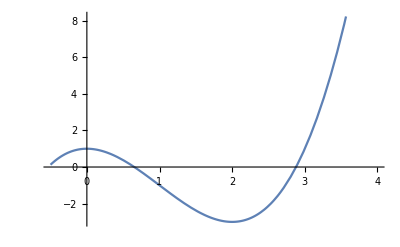

-6 x+3 x^2

{{x→0},{x→2}}

0

2

1

-3

3/8

17

```mathematica
Clear[x]
Clear[f]
Clear[fPrime]
f[x_]=x^3-3 x^2+1
Plot[f[x],{x,-1/2,4}]
fPrime[x_]=Dt[f[x],x]
criticalN=Solve[fPrime[x]==0,x]
criticalN[[1,1,2]]
criticalN[[2,1,2]]
f[criticalN[[1,1,2]]]
f[criticalN[[2,1,2]]]
f[1/2]
f[4]
```

3.2 THE MEAN VALUE THEOREM

## FERMAT’S THEOREM

### -Graphics-

### -Graphics-

### -Graphics-

#### -Graphics- -Graphics--Graphics-